# Photon orbits and Poincare sections in a Hartle-Thorne spacetime

George Pappas
AUTh, Thessaloniki, Greece

This notebook accompanies the paper “Chaotic photon orbits and shadows of a non-Kerr object described by the Hartle-Thorne spacetime” (arXiv:2111.09367 [gr-qc]) and gives a demonstration of some of the calculations present in the paper.

Specifically the notebook solves the equations of motion for null particles in a Hartle-Thorne background spacetime at O(ε^2) in rotation end extracts a Poincare section under specified conditions.

At first, we define the HT spacetime that we will use and then give the setup for the Hamiltonian formulation for the equations of motion. We then integrate these equations and extract the Poincare section or the required orbit.

## Definitions for the spacetime

Here we define the Hartle-Thorne spacetime at O(ε^2) in rotation. The metric functions are first given as expansions and then we fix the order and assume the metric as it is in terms of the mass M, the spin parameter a=J/M and quadrupole deformation δq. We generally assume M=1, which defines the scale of the problem. In the end we set the bookkeeping parameter ε to 1.

```mathematica
Quit[];
```

#### The Hartle-Thorne metric

```mathematica
gHtt2=Normal[Series[-(1-(2M)/r)(1+ε^2 (2h0+2h2 LegendreP[2,Cos[θ]]))+r^2 Sin[θ]^2  ε^2 (Ω-ω1  D[LegendreP[1,Cos[θ]],Cos[θ]])^2,{ε,0,2}]]
gHrr2=Normal[Series[(1-(2M)/r)^-1(  1+(2 ε^2 (μ0+μ2  LegendreP[2,Cos[θ]]))/(r-2M)),{ε,0,2}]];
gHθθ2=Normal[Series[r^2 (1+2 ε^2 k2 LegendreP[2,Cos[θ]]),{ε,0,2}]];
gHφφ2=Normal[Series[r^2 Sin[θ]^2 (1+2 ε^2 k2 LegendreP[2,Cos[θ]]),{ε,0,2}]];
gHtφ2=Normal[Series[-r^2 Sin[θ]^2 ((1+2 ε^2 k2  LegendreP[2,Cos[θ]]) ε (Ω-ω1 D[LegendreP[1,Cos[θ]],Cos[θ]]+ε^2 (ζ1 D[LegendreP[1,Cos[θ]],Cos[θ]]+ζ3 D[LegendreP[3,Cos[θ]],Cos[θ]]))),{ε,0,2}]];
```

-1+(2 M)/r+ε^2 ((-1+(2 M)/r) (2 h0+h2 (-1+3 Cos[θ]^2))+r^2 (Ω-ω1)^2 Sin[θ]^2)

```mathematica
h0=a^2/(x^3(x-2))/.{x-> r/M};
h2= 1/4 a^2 5/4 δq (1-2/x)( 3 x^2 Log[1-2/x]+2/x(3 x^2-6x-2)(1-1/x)/(1-2/x)^2)+ a^2/x^3(1+1/x)/.{x->r/M};
μ0=-(M a^2)/x^3 /.{x-> r/M};
μ2= (r-2M) ( -h2 + (6 S^2)/r^4) /.{S-> M^2 a};
k2=-a^2/x^3(1+2/x)- 1/2 a^2  5/4 δq ( - 3(1- x^2/2)Log[1-2/x]-2/x + 3(1+x))/.{x-> r/M};
ω1=Ω -(2a)/(M x^3)/.{x-> r/M};
ζ1=a^3/(10M x^6)( -8(1+3/x) +  x^2 5/4 δq( 3x(x-2) (5 x^2-2x -4)Log[1-2/x] + 2(15 x^3-21 x^2 -16 x +6)  ) )/.{x-> r/M};
ζ3=-a^3/(15M x^5)( 2(1-2/x)(5+9/x) +  1/2 x  5/4 δq( 3/2 x(x-2) (105 x^4-140 x^3 -12x -4)Log[1-2/x] +  315 x^5-735 x^4+210 x^3 +34 x^2 +52 x +36)-15/16 x^2 δs3(  35/2 x^3(x-2) (3x -4)Log[1-2/x]  + 7/3(45 x^4-105 x^3 +30 x^2 +10 x +4) )  ) /.{x->r/M};
```

```mathematica
gHT2=Simplify[{gtφ[r,θ]->gHtφ2 , Derivative[1,0][gtφ][r,θ]->D[ gHtφ2,r] ,Derivative[0,1][gtφ][r,θ]->  D[gHtφ2,θ],gφφ[r,θ]-> gHφφ2,Derivative[0,1][gφφ][r,θ]->  D[gHφφ2,θ],Derivative[1,0][gφφ][r,θ]-> D[ gHφφ2,r],gtt[r,θ]-> gHtt2, Derivative[0,1][gtt][r,θ]-> D[gHtt2,θ], Derivative[1,0][gtt][r,θ]-> D[gHtt2,r],gθθ[r,θ]->gHθθ2,Derivative[1,0][gθθ][r,θ]-> D[gHθθ2,r],Derivative[0,1][gθθ][r,θ]-> D[gHθθ2,θ], grr[r,θ]-> gHrr2,Derivative[1,0][grr][r,θ]->D[gHrr2,r], Derivative[0,1][grr][r,θ]-> D[gHrr2,θ]}]//.{ε->1};
```

## Setting up the equations of motion

Here we produce the equations of motion for the photons. We start from the integrals of motion and then we define first the Lagrangian and then the Hamiltonian for the equations of motion. Here the equations of motion are expressed in terms of the conjugate momenta p_r, p_θ, the positions x^a and the velocities dr/dλ, dt/dλ.

```mathematica
constRep=Solve[{-Ee==gtt tdot+gtφ φdot,Le==gtφ tdot+gφφ φdot},{tdot,φdot}][[1]]
```

{tdot→-(-Ee gφφ-gtφ Le)/(gtφ^2-gtt gφφ),φdot→-(Ee gtφ+gtt Le)/(gtφ^2-gtt gφφ)}

```mathematica
Lagran=1/2 (gtt tdot^2+2 gtφ tdot φdot+grr rdot^2+gθθ θdot^2+gφφ φdot^2)
```

1/2 (grr rdot^2+gtt tdot^2+gθθ θdot^2+2 gtφ tdot φdot+gφφ φdot^2)

```mathematica
constRep2=Solve[{D[Lagran,rdot]==pr,D[Lagran,θdot]==pθ,D[Lagran,φdot]==Le,D[Lagran,tdot]==-Ee},{tdot,φdot,rdot,θdot}][[1]]
```

{tdot→-(-Ee gφφ-gtφ Le)/(gtφ^2-gtt gφφ),φdot→-(-Ee gtφ-gtt Le)/(-gtφ^2+gtt gφφ),rdot→pr/grr,θdot→pθ/gθθ}

```mathematica
Hamilt=FullSimplify[-Ee tdot+Le φdot+grr rdot^2+gθθ θdot^2-Lagran//.constRep2]
```

1/2 ((Ee^2 gφφ+2 Ee gtφ Le+gtt Le^2)/(-gtφ^2+gtt gφφ)+pr^2/grr+pθ^2/gθθ)

```mathematica
Hamilt==0
```

1/2 ((Ee^2 gφφ+2 Ee gtφ Le+gtt Le^2)/(-gtφ^2+gtt gφφ)+pr^2/grr+pθ^2/gθθ)==0

```mathematica
ruleAffine2={pr-> pr[λ],pθ-> pθ[λ],r-> r[λ],θ-> θ[λ],pt-> pt[λ],pφ-> pφ[λ],rdot->r'[λ],θdot->θ'[λ],tdot->t'[λ],φdot->φ'[λ],prdot->pr'[λ],pθdot->pθ'[λ],ptdot->pt'[λ],pφdot->pφ'[λ]};
```

```mathematica
ruleMetric={gtt-> gtt[r,θ],gtφ->gtφ[r,θ],grr-> grr[r,θ],gθθ-> gθθ[r,θ],gφφ-> gφφ[r,θ]}
```

{gtt→gtt[r,θ],gtφ→gtφ[r,θ],grr→grr[r,θ],gθθ→gθθ[r,θ],gφφ→gφφ[r,θ]}

```mathematica
Hamilt2=Hamilt/.ruleMetric
```

1/2 (pr^2/grr[r,θ]+pθ^2/gθθ[r,θ]+(Le^2 gtt[r,θ]+2 Ee Le gtφ[r,θ]+Ee^2 gφφ[r,θ])/(-gtφ[r,θ]^2+gtt[r,θ] gφφ[r,θ]))

```mathematica
eqSyst={rdot==D[Hamilt2,pr],θdot==D[Hamilt2,pθ],prdot==-D[Hamilt2,r],pθdot==-D[Hamilt2,θ],tdot==-(-Ee gφφ-gtφ Le)/(gtφ^2-gtt gφφ)/.ruleMetric,φdot==-(Ee gtφ+gtt Le)/(gtφ^2-gtt gφφ)/.ruleMetric,ptdot==0,pφdot==0}
```

{rdot==pr/grr[r,θ],θdot==pθ/gθθ[r,θ],prdot==1/2 ((pr^2 grr^(1,0)[r,θ])/grr[r,θ]^2+(pθ^2 gθθ^(1,0)[r,θ])/gθθ[r,θ]^2-(Le^2 gtt^(1,0)[r,θ]+2 Ee Le gtφ^(1,0)[r,θ]+Ee^2 gφφ^(1,0)[r,θ])/(-gtφ[r,θ]^2+gtt[r,θ] gφφ[r,θ])+((Le^2 gtt[r,θ]+2 Ee Le gtφ[r,θ]+Ee^2 gφφ[r,θ]) (gφφ[r,θ] gtt^(1,0)[r,θ]-2 gtφ[r,θ] gtφ^(1,0)[r,θ]+gtt[r,θ] gφφ^(1,0)[r,θ]))/(-gtφ[r,θ]^2+gtt[r,θ] gφφ[r,θ])^2),pθdot==1/2 ((pr^2 grr^(0,1)[r,θ])/grr[r,θ]^2+(pθ^2 gθθ^(0,1)[r,θ])/gθθ[r,θ]^2-(Le^2 gtt^(0,1)[r,θ]+2 Ee Le gtφ^(0,1)[r,θ]+Ee^2 gφφ^(0,1)[r,θ])/(-gtφ[r,θ]^2+gtt[r,θ] gφφ[r,θ])+((Le^2 gtt[r,θ]+2 Ee Le gtφ[r,θ]+Ee^2 gφφ[r,θ]) (gφφ[r,θ] gtt^(0,1)[r,θ]-2 gtφ[r,θ] gtφ^(0,1)[r,θ]+gtt[r,θ] gφφ^(0,1)[r,θ]))/(-gtφ[r,θ]^2+gtt[r,θ] gφφ[r,θ])^2),tdot==-(-Le gtφ[r,θ]-Ee gφφ[r,θ])/(gtφ[r,θ]^2-gtt[r,θ] gφφ[r,θ]),φdot==-(Le gtt[r,θ]+Ee gtφ[r,θ])/(gtφ[r,θ]^2-gtt[r,θ] gφφ[r,θ]),ptdot==0,pφdot==0}

```mathematica
eqSyst2=eqSyst/.ruleAffine2;
```

## Trajectories and Poincare sections

Here we will first give the separatrix for specific values for the metric parameters (rotation and quadrupole) and some value of the impact parameter. Then we will calculate some orbits solving the initial value problem . In the end we will produce a Poincare section for a set of initial conditions so as to populate the regions of interest.  
The value we choose for the impact parameter is one that corresponds to a closed system.

### Separatrix b=4.3048 (open at b=4.304332) for a=0.327352 and δq=1

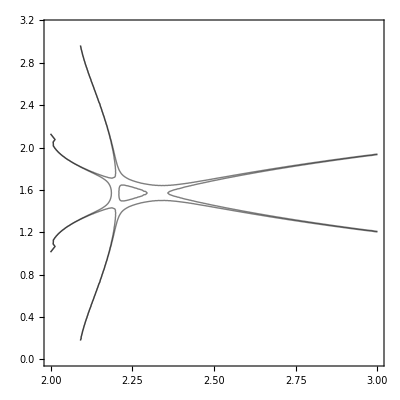

```mathematica
separFunct=Simplify[(Le^2 gtt[r,θ]+2 Ee Le gtφ[r,θ]+Ee^2 gφφ[r,θ])/(gtφ[r,θ]^2-gtt[r,θ] gφφ[r,θ])/.gHT2//.{M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}];
ContourPlot[separFunct,{r,2,3},{θ,0,π},Contours->{0,-0.01},ContourShading->False]
```

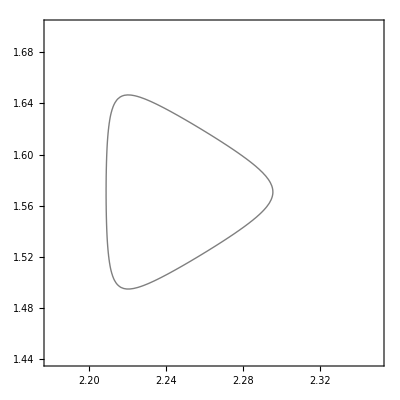

```mathematica
separPlot=ContourPlot[separFunct,{r,2.18,2.35},{θ,1.44,1.7},Contours->{0},ContourShading->False,PlotPoints->50]
```

### Trajectory

Here we first call some packages and define an integration method, that we will use to NDSolve the equations of motion. Then we choose three initial conditions and calculate three trajectories which we show in the (r,θ) plane (the second trajectory is also shown in (x,y,z)).

```mathematica
(*<< NumericalMath`EquationTrekker`*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
(*Needs["Graphics`"];*)
Needs["GUIKit`"];
Off[NDSolve::noout];
```

```mathematica
ImplicitMidpoint ={"FixedStep", Method->{"ImplicitRungeKutta","Coefficients"->"ImplicitRungeKuttaGaussCoefficients", "DifferenceOrder"->2,"ImplicitSolver"->{"FixedPoint","AccuracyGoal"->MachinePrecision,"PrecisionGoal"->MachinePrecision,"IterationSafetyFactor"->1 }}};
ImplicitMidpoint4 ={"FixedStep", Method->{"ImplicitRungeKutta","Coefficients"->"ImplicitRungeKuttaGaussCoefficients", "DifferenceOrder"->4,"ImplicitSolver"->{"FixedPoint","AccuracyGoal"->MachinePrecision,"PrecisionGoal"->MachinePrecision,"IterationSafetyFactor"->1 }}};
```

```mathematica
gHT22=gHT2/.ruleAffine2;
varH={t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]}
Off[NDSolve::noout];
```

{t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]}

```mathematica
systemEqH=eqSyst2/.gHT22//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048};
varH={t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]}
Off[NDSolve::noout];
```

{t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]}

These are three initial conditions that lead to different types of orbits. The pairs are (r,p_r) on the equatorial plane θ=π/2.

```mathematica
{{2.225275868879109,0.0006629712219409778},{2.2394826563166657,-0.06628659632084594},{2.2611122486843076,0.02886147708238801}}
```

```mathematica
Solve[0==Hamilt2//.{pr->0}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2,r->2.225275},pθ]
```

{{pθ→-0.109182},{pθ→0.109182}}

```mathematica
Solve[0==Hamilt2//.{pr->-0.066286}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2,r->2.23948},pθ]
```

{{pθ→-0.107323},{pθ→0.107323}}

```mathematica
Solve[0==Hamilt2//.{pr->0.028861477}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2,r->2.261112},pθ]
```

{{pθ→-0.101956},{pθ→0.101956}}

1st trajectory

```mathematica
inValH={r[0]==2.225275,t[0]==0,φ[0]==0,θ[0]==π/2,pt[0]==-Ee,pφ[0]==b Ee,pr[0]==0,pθ[0]==(pθ/.{pθ->0.10918215315166532})}//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048};
```

```mathematica
fullSystem=Normal[Flatten[{systemEqH,inValH}]];
λf=1000;Timing[solHTtragect1=NDSolve[fullSystem,{t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]},{λ,0,λf},MaxSteps->Infinity,Method->ImplicitMidpoint, StartingStepSize->1/100];]
```

{1.70656,Null}

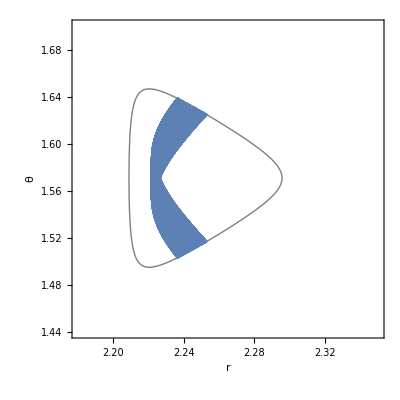

```mathematica
Show[separPlot,ParametricPlot[Evaluate[{r[λ] ,θ[λ]}/.solHTtragect1],{λ,0,1000},PlotRange->{{2.18,2.35},{1.44,1.7}},AspectRatio->1,Axes->False,Frame->True],FrameLabel->{"r","θ"},BaseStyle->{FontSize->18,FontFamily->"Times"}]
```

2nd trajectory

```mathematica
inValH={r[0]==2.23948,t[0]==0,φ[0]==0,θ[0]==π/2,pt[0]==-Ee,pφ[0]==b Ee,pr[0]==-0.066286,pθ[0]==(pθ/.{pθ->0.1073231351993825})}//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048};
```

```mathematica
fullSystem=Normal[Flatten[{systemEqH,inValH}]];
λf=1000;Timing[solHTtragect2=NDSolve[fullSystem,{t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]},{λ,0,λf},MaxSteps->Infinity,Method->ImplicitMidpoint, StartingStepSize->1/100];]
```

{1.6636,Null}

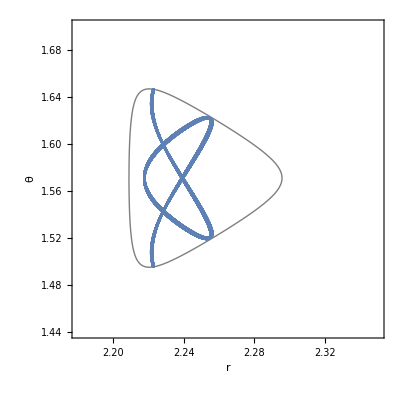

```mathematica
Show[separPlot,ParametricPlot[Evaluate[{r[λ] ,θ[λ]}/.solHTtragect2],{λ,0,1000},PlotRange->{{2.18,2.35},{1.44,1.7}},AspectRatio->1,Axes->False,Frame->True],FrameLabel->{"r","θ"},BaseStyle->{FontSize->18,FontFamily->"Times"}]
```

```mathematica
ParametricPlot3D[Evaluate[{r[λ] Sin[θ[λ]] Cos[φ[λ]],r[λ] Sin[θ[λ]] Sin[φ[λ]],r[λ] Cos[θ[λ]]}/.solHTtragect2],{λ,0,50},PlotRange->All,AxesLabel->{"x","y","z"},PlotPoints->100,BaseStyle->{FontSize->18,FontFamily->"Times"},BoxRatios->{1,1,1}]
```

-Graphics3D-

3rd trajectory

```mathematica
inValH={r[0]==2.261112,t[0]==0,φ[0]==0,θ[0]==π/2,pt[0]==-Ee,pφ[0]==b Ee,pr[0]==0.028861477,pθ[0]==(pθ/.{pθ->0.10195640252777025})}//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048};
```

```mathematica
fullSystem=Normal[Flatten[{systemEqH,inValH}]];
λf=1000;Timing[solHTtragect3=NDSolve[fullSystem,{t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]},{λ,0,λf},MaxSteps->Infinity,Method->ImplicitMidpoint, StartingStepSize->1/100];]
```

{1.5566,Null}

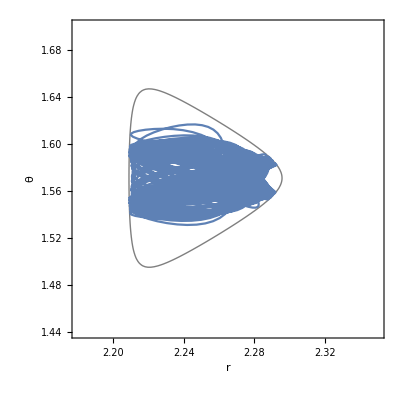

```mathematica
Show[separPlot,ParametricPlot[Evaluate[{r[λ] ,θ[λ]}/.solHTtragect3],{λ,0,1000},PlotRange->{{2.18,2.35},{1.44,1.7}},AspectRatio->1,Axes->False,Frame->True],FrameLabel->{"r","θ"},BaseStyle->{FontSize->18,FontFamily->"Times"}]
```

### Poincare section

Here we first define a set of initial conditions in the appropriate range. Then we define a function that will integrate these initial conditions and extract the Poincare section. The section is plotted in the (r,p_r) plane and it is taken for θ=π/2 and p_θ>0.
The Poincare section takes around 500 seconds to evaluate for the set of initial conditions we have and for an affine time of integration of 10,000 units.

```mathematica
{{"2.294","1.572"},{"2.21","1.57"}}
```

```mathematica
Solve[0==Hamilt2//.{pr->0}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2,r->2.2115},pθ]
Solve[0==Hamilt2//.{pr->0}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2,r->2.294},pθ]
```

{{pθ→-0.0523945},{pθ→0.0523945}}

{{pθ→-0.0216335},{pθ→0.0216335}}

```mathematica
inValTab=Flatten[{Table[{r,pθ/.Solve[0==Hamilt2//.{pr->0}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2},pθ][[2]],0},{r,2.2115,2.294,(2.294-2.2115)/15}],Table[{r,pθ/.Solve[0==Hamilt2//.{pr->0.05}/.gHT2//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048}/.{θ->π/2},pθ][[2]],0.05},{r,2.21966,2.2706,(2.2706-2.21966)/10}]},1]
%//Dimensions
```

{{2.2115,0.0523945,0},{2.217,0.0859509,0},{2.2225,0.103411,0},{2.228,0.113441,0},{2.2335,0.118718,0},{2.239,0.120545,0},{2.2445,0.119679,0},{2.25,0.11661,0},{2.2555,0.111663,0},{2.261,0.105055,0},{2.2665,0.0969069,0},{2.272,0.0872467,0},{2.2775,0.0759642,0},{2.283,0.0626878,0},{2.2885,0.0463213,0},{2.294,0.0216335,0},{2.21966,0.0867079,0.05},{2.22475,0.100327,0.05},{2.22985,0.108204,0.05},{2.23494,0.112178,0.05},{2.24004,0.113212,0.05},{2.24513,0.111884,0.05},{2.25022,0.108567,0.05},{2.25532,0.103501,0.05},{2.26041,0.0968256,0.05},{2.26551,0.0885829,0.05},{2.2706,0.07869,0.05}}

{27,3}

```mathematica
systemEqH=eqSyst2/.gHT22//.{ε->1,M->1,a->0.327352,δq->1,Le->b Ee, Ee->1,b->4.3048};
varH={t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]}
Off[NDSolve::noout];
```

{t[λ],φ[λ],r[λ],θ[λ],pt[λ],pφ[λ],pr[λ],pθ[λ]}

```mathematica
λf=10000;
icvars=varH/.λ->0 ;
psect[ics_] := 
Module[{reapdata},reapdata=
Reap[NDSolve[{systemEqH,Thread[icvars == ics]},{},{λ,λf},MaxSteps->Infinity,Method->{"EventLocator","Event"->θ[λ]-π/2,"EventAction":> If[pθ[λ]>0,Sow[{r[λ], pr[λ]}],Null],"EventLocationMethod"->"LinearInterpolation","Method"->ImplicitMidpoint}, StartingStepSize->1/100];];If[reapdata=={Null,{}},{Sow[{Null,Null}]},reapdata[[-1,1]]]
];
```

{462.182,Null}

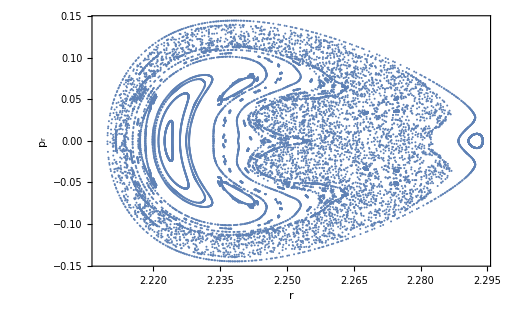

```mathematica
{t[0]==0,φ[0]==0,r[0]==r0,θ[0]==π/2,pt[0]==-1,pφ[0]==4.3048,pr[0]==pr0,pθ[0]==pθ0};
Timing[data5 = 
Flatten[
Map[psect, Table[{0,0,inValTab[[i,1]],π/2,-1,4.3048,inValTab[[i,3]],inValTab[[i,2]]},{i,1,27}]], 
1];]
ListPlot[data5,Axes->False,Frame->True,FrameLabel->{"r","p_r"},BaseStyle->{FontSize->18,FontFamily->"Times"}]
(*Export["Im_P_Section - E="<>ToString[-0.52]<>" - Lz="<>ToString[pφ0[[1]]]<>".txt",data,"Table"]*)
```